# A Machine Learning Analysis of Halting in the SKI Combinator Calculus

Euan Ong

Much of machine learning is driven by the question: can we learn what we cannot compute? The learnability of the halting problem, the canonical undecidable problem, to an arbitrarily high accuracy for Turing machines was proven by Lathrop (Lathrop, 1996). The SKI combinator calculus can be seen as a reduced form of the untyped lambda calculus, which is Turing-complete (Turing, 1937); hence, the SKI combinator calculus forms a universal model of computation. In this vein, we analyse the growth and halting times of SKI combinator expressions, estimate the probability of an SKI combinator expression halting after a given number of steps, and investigate the feasibility of a machine learning approach to predicting whether a given SKI combinator expression is likely to halt.

## SK Combinators

What we will refer to as ‘SK Combinators’ are expressions in the SKI combinator calculus,  a simple Turing-complete language introduced by Schönfinkel (1924) and Curry (1930). In the same way that NAND gates can be used to construct any expression in Boolean logic, SK combinators were posed as a way to construct any expression in predicate logic, and being a reduced form of the untyped lambda calculus, any functional programming language can be implemented by a machine that implements SK combinators. While implementations of this language exist, these serve little functional purpose - instead, this language, a simple idealisation of transformations on symbolic expressions [NKS], provides a useful tool for studying complex computational systems.

### Rules and Expressions

Formally, SK combinator expressions are binary trees whose leaves are labelled either 'S', 'K' or 'I': each tree (xy) represents a function x applied to an argument y. When the expression is evaluated (i.e. when the function is applied to the argument), the tree is transformed into another tree, the 'value'. The basic 'rules' for evaluating combinator expressions are given below:

k[x_][y_] := x

The K combinator or ‘constant function’: when applied to x, returns the function k[x], which when applied to some y will return x.

s[x_][y_][z_] := x[z][y[z]]

The S combinator or ‘fusion function’: when applied to x, y, z, returns x applied to z, which is in turn applied to the result of y applied to z.

i[x_] := x

The I combinator or ‘identity function’: when applied to x, returns x.

Note that the I combinator I[x] is equivalent to the function S[K][a][x], as the latter will evaluate to the former in two steps:

S[K][a][x]
= K[x][a[x]]
= x

Thus the I combinator is redundant as it is simply ‘syntactic sugar’ - for the purposes of this exploration it will be ignored.

These rules can be expressed in the Wolfram Language as follows:

```mathematica
SKRules={k[x_][y_]:> x,s[x_][y_][z_]:> x[z][y[z]]}
```

{k[x_][y_]:>x,s[x_][y_][z_]:>x[z][y[z]]}

### Evaluation

The result of applying these rules to a given expression is given by the following functions:

```mathematica
SKNext[expr_]:=expr/.SKRules;
```

Returns the next ‘step’ of evaluation of the expression expr - evaluating all functions in expr according to the rules above without evaluating any ‘new’/transformed functions.

```mathematica
SKEvaluate[expr_,n_]:=NestList[#1/.SKRules&,expr,n];
```

Returns the next n steps of evaluation of the expression expr

```mathematica
SKEvaluateUntilHalt[expr_,n_] := FixedPointList[SKNext,expr,n+1];
```

Returns the steps of evaluation of expr until either it reaches a fixed point or it has been evaluated for n steps, whichever comes first.

Note that, due to the Church-Rosser theorem, the order in which the rules are applied does not affect the final result, as long as the combinator evaluates to a fixed point / ‘halts’. For combinators with no fixed point, which do not halt, the behaviour demonstrated as they evaluate could change based on the order of application of the rules - this is not explored here and is a topic for potential future investigation.

### Examples

The functions above can be used to evaluate a number of interesting SK combinator expressions:

```mathematica
Column[SKEvaluateUntilHalt[s[k][a][x],10][[1;;-2]]]
```

s[k][a][x]
k[x][a[x]]
x

The I combinator

```mathematica
Column[SKEvaluateUntilHalt[s[k[s[i]]][k][a][b],10][[1;;-2]]]
```

s[k[s[i]]][k][a][b]
k[s[i]][a][k[a]][b]
s[i][k[a]][b]
b[k[a][b]]
b[a]

The reversal expression - s[k][s[i]][k][a][b] takes two terms, a and b, and returns b[a].

## Growth and Halting

### Halting

### E <Write about SKI combinators and what halting means - nb, we are not trying to *solve* the *halting problem* which is undecidable. Talk about https://www.ics.uci.edu/~rickl/publications/1996-icml.pdf> https://en.wikipedia.org/wiki/Unlambda

### Rasterization - add examples

```mathematica
SKRasterize[func_]:=SKRasterize[func,10];
SKRasterize[func_,n_]:=Module[{SKRules,SKEvaluate,SKArray,SKGrid},
SKRules={k[x_][y_]:> x,s[x_][y_][z_]:> x[z][y[z]]};
SKEvaluate[expr_]:=NestList[#1/.SKRules&,expr,n];
SKArray[expr_]:=Characters/@ToString/@SKEvaluate[expr];
SKGrid[exp_]:=ArrayPlot[SKArray[exp],{ColorRules->{"s"->RGBColor[1,0,0],"k"->RGBColor[0,1,0],"["->RGBColor[0,0,1],"]"->RGBColor[0,0,0]},PixelConstrained->True,Frame->False,ImageSize->1000}];
SKGrid[func]
]
```

```mathematica
SKRules={k[x_][y_]:> x,s[x_][y_][z_]:> x[z][y[z]]};
SKEvaluate[expr_,n_]:=NestList[#1/.SKRules&,expr,n];
SKEvaluate[expr_]:=SKEvaluate[expr,10];
SKArray[expr_]:=SKArray[expr,10];
SKArray[expr_,n_]:=Characters/@ToString/@SKEvaluate[expr,n];
SKGrid[exp_]:=SKGrid[exp,10];
SKGrid[exp_,n_]:=ArrayPlot[SKArray[exp,n],{ColorRules->{"s"->RGBColor[1,0,0],"k"->RGBColor[0,1,0],"["->RGBColor[0,0,1],"]"->RGBColor[0,0,0]},PixelConstrained->True,Frame->False,ImageSize->1000}];
SKRasterize[func_]:=SKRasterize[func,10];
```

```mathematica
SKRasterize[func_,n_]:=SKGrid[func,n]
```

```mathematica
SKLengths[exp_,n_]:=StringLength/@ToString/@SKEvaluate[exp,n];
```

```mathematica
SKRasterize[s[s][k][s[s[s][k]]][k]]
```

-Graphics-

```mathematica
SKFuncs = {s[s[s]][s][k][k],s[s[s]][s][s][s],s[s[s]][s][s][s][k],s[s][s][s[s[s]]][s],s[s[s]][s][s][s][s],s[s[s]][s][s][s][s],s[s][s][s[s[s[s]]]][k],s[s][k][s[s[s]]][s][k],s[s][s][s[s[s]]][s][k],s[s][s][s[s]][s][s[k]],s[s[s[s][s]]][s][s][k],s[s][k][s[s[s][k]]][k]}
```

{s[s[s]][s][k][k],s[s[s]][s][s][s],s[s[s]][s][s][s][k],s[s][s][s[s[s]]][s],s[s[s]][s][s][s][s],s[s[s]][s][s][s][s],s[s][s][s[s[s[s]]]][k],s[s][k][s[s[s]]][s][k],s[s][s][s[s[s]]][s][k],s[s][s][s[s]][s][s[k]],s[s[s[s][s]]][s][s][k],s[s][k][s[s[s][k]]][k]}

```mathematica
SKRasterize/@SKFuncs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Random SK combinators ()

## Investigating growth of SK combinators

### Halting Graphs

SKLengths generates a table of length of combinator

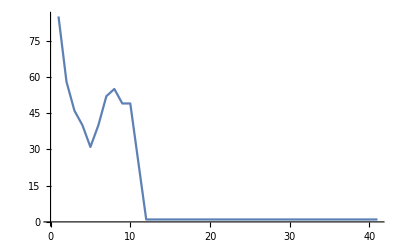

```mathematica
ListLinePlot[SKLengths[k[k[k[k[s[s[s]]]][s]][k[s][k]][s[k]][k]][k[s[k[k]][s]][k[k]][k]][s[k[k[k]]]][s[s]][s],40]]
```

```mathematica
exprs = Table[RandomSKExpr[40],10];
ImageCollage[Table[ListLinePlot[SKLengths[exprs[[n]],40]],{n,10}]]
```

-Graphics-

### Halting Probabilities

Some halt, some do not. (haven’t seen a cyclical one yet) --> linear/exponential.
Assumptions: If length stays constant, it has halted. Dataset: SK combinators with depth 10
P(halts by 20|doesn’t halt by 10) = ? P(halts by 30|doesn’t halt by 20

```mathematica
exprs = Monitor[Table[RandomSKExpr[10],{n,100}],n];
```

```mathematica
lengths = Monitor[Table[SKLengths[exprs[[n]],40],{n,100}],n];
```

$Aborted

```mathematica
HaltIf[n_,list_]:=SameQ[list[[n]],list[[n-1]]]
```

```mathematica
HaltBy[n_,lens_]:=Count[lens,x_/;HaltIf[n,x]==True]
```

Taking only lengths:

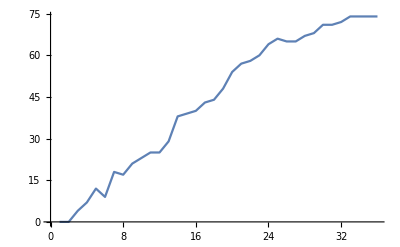

```mathematica
ListLinePlot[Table[HaltBy[n,lengths],{n,0,35}]]
```

Number that have ‘constant length’ after every 5 iterations (c.f. nuclear half life?)

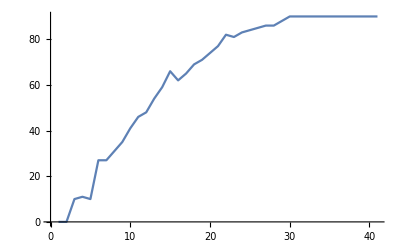

Number that have halted after every 5 iterations (checking for actual halting)

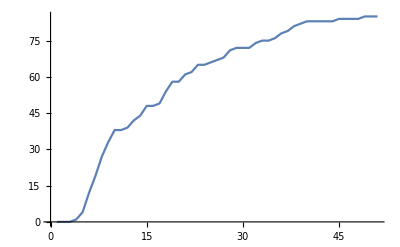

A sample of 1000 combinators, generated with a recursive random function (generating combinators of different length)

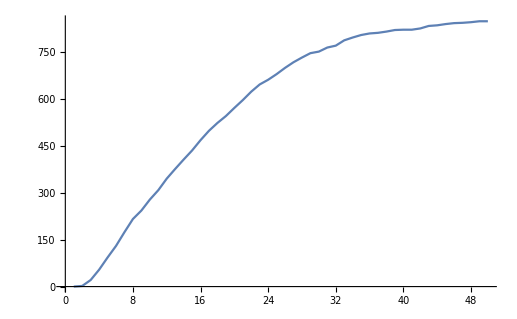

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

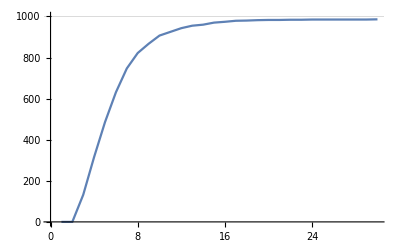
{1.30911,-Graphics-}

```mathematica
CloudEvaluate[GenerateHaltGraph[20,30,1000]]//AbsoluteTiming
```

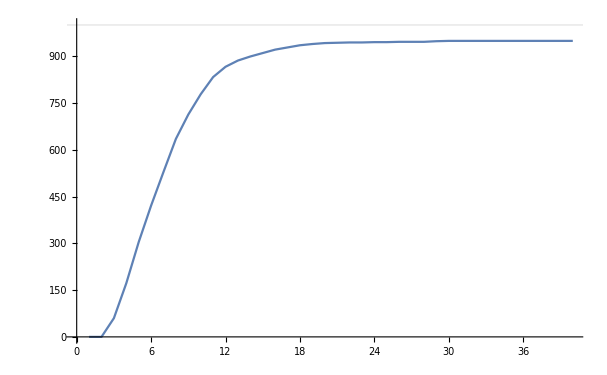
{178.927,-Graphics-}

```mathematica
GenerateHaltGraph[30,40,1000]//AbsoluteTiming
```

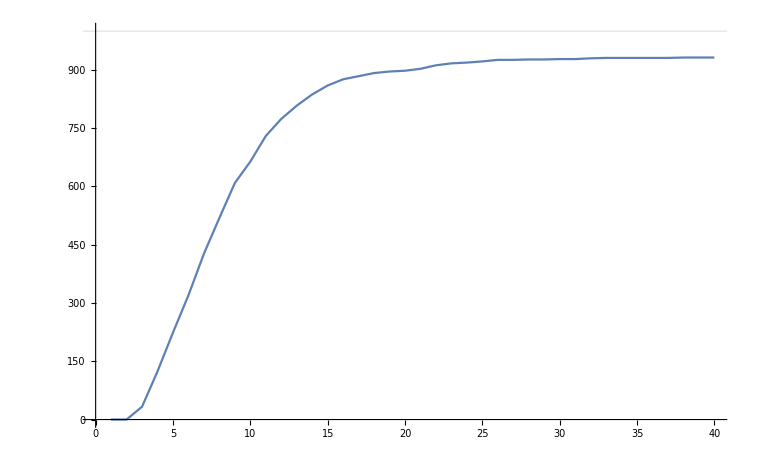
{37.7255,-Graphics-}

```mathematica
CloudEvaluate[GenerateHaltGraph[40,40,1000]]//AbsoluteTiming
```

#### How many combinators with a given leaf size?

NKS suggests (2^n*((2n-2)C(n-1)))/n
So for size 30:

```mathematica
CountCombinators[n_]:=2^n Binomial[2n-2,n-1]/n
```

```mathematica
CountCombinators[30]
```

1076149385797043048415232

## Machine Learning Analysis of SK Combinators

### Generating Datasets

#### ~500*n random SK expressions at each of depths {n,1,10}, halted if SKHalt[40]==True.

```mathematica
Monitor[Table[x=GenerateTable[n,40,n*500];DumpSave["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/SK-Combinators/"<>ToString[n]<>".mx",x],{n,1,50}],n] (*generate all possible expressions*)
```

#### ~1000*n random SK expressions at depth 50, halted if SKHalt[40]==True. New random algorithm

```mathematica
x=GenerateTable[50,100,20000];DumpSave["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/SK-Combinators/10_40_10000_randomnew.mx",x];
```

#### ~1000 random SK expressions at depth 40, halted if SKHalt[40]==True. New random algorithm

```mathematica
Clear[x]
```

```mathematica
x=GenerateTable[40,40,1000];DumpSave["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/SK-Combinators/10_d40_40_10000_randomnew.mx",x];
```

#### ~1000 random SK expressions at depth 30, halted if SKHalt[40]==True. New random algorithm

```mathematica
Clear[x]
```

```mathematica
x=GenerateTable[30,40,1000];DumpSave["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/SK-Combinators/10_d30_40_10000_randomnew.mx",x];
```

#### ~5000 random SK expressions at depth 10, halted if SKHalt[40] == True.

```mathematica
x=GenerateTable[10,40,1000];DumpSave["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/SK-Combinators/10_40.mx",x];
```

```mathematica
x=GenerateTable[10,40,5000];DumpSave["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/SK-Combinators/10_40_test.mx",x];
```

$Aborted

#### ~5000 random SK expressions at depth 8, halted if SKHalt[40] == True.

```mathematica
x=GenerateTable[8,40,5000];DumpSave["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/SK-Combinators/8_40.mx",x];
```

```mathematica
x=GenerateTable[8,40,5000];DumpSave["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/SK-Combinators/8_40_test.mx",x];
```

### Training Attempt #1: 1000 random SK expressions, depth 10, halted if SKHalt[40]==True. NoHalt dataset same length as Halt dataset. Using raw string. Best classifier so far.

```mathematica
lengths = GenerateTable[10,40,1000]
```

```mathematica
NoHalt = Select[lengths,#[[2]]==False&]
Halt = Select[lengths,#[[2]]==True&]
HaltTrain = RandomSample[Halt,Length[NoHalt]]
TrainingData = Join[HaltTrain,NoHalt]
TrainingData2 = ConvertSKTableToString[TrainingData]
```

```mathematica
HaltClassifier1 = Classify[TrainingData2]
```

```mathematica
HaltClassifier1["s[s[s]][s][s][s][k]"]
```

True

#### Classifier test:

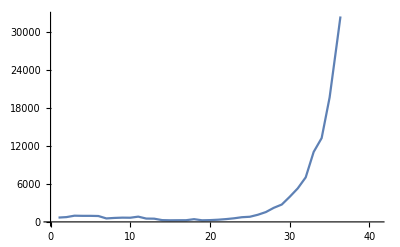
{False,-Graphics-}

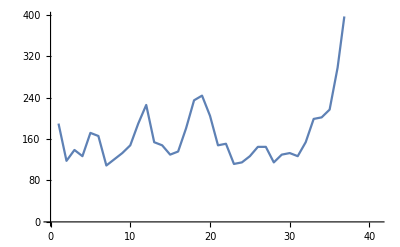
{False,-Graphics-,False}

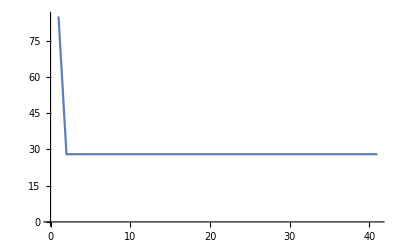
{True,-Graphics-,False}

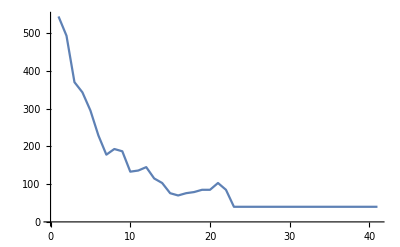
{True,-Graphics-}

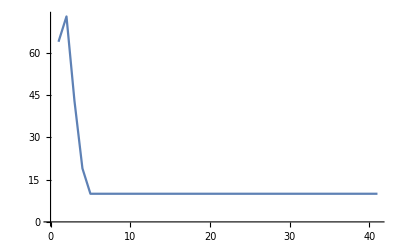
{True,-Graphics-}

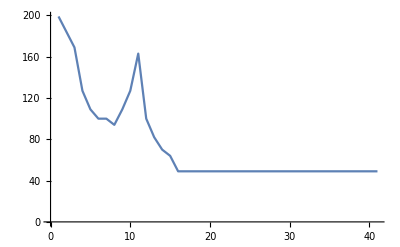
{True,-Graphics-}

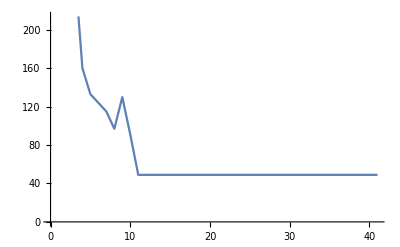
{True,-Graphics-}

```mathematica
Table[TestClassifier[HaltClassifier1,TrainingData2],10]
```

```mathematica
SKGrid[k[s[k[k[k[k[s[s[k[k[k[k][s[s[k[k[s[s][k[k[k][k[k[s[k]]]]][k[k]][s]]]]][k[s]]]][k[s[k[k][k[s[k[s[s][s[s]]]][s[s[k]]]][k]]][s[s[k[k]]]][k[k]]]][s[k[s[s[k][s[k][k]][s[k]]]][k[s[k]][k]]][s[k]][k]]][s[k[s]][k]][k[k[k]]]][k]]]]]]][k[s[s[k[s[s]]]]][s]]][k[s]]]]
```

-Graphics-

```mathematica
GenerateTable[depth_,iterations_,number_]:=Module[{exprs},
exprs = Monitor[Table[RandomSKExpr[depth],{n,number}],n];
lengths = Monitor[Table[exprs[[n]]-> SKHalt[exprs[[n]],iterations],{n,number}],n];
Return[lengths]
]
```

```mathematica
Monitor[Flatten[Table[GenerateTable[n,40,200],{n,1,10}]],n]
```

{k[s]→True,s[k]→True,1997,s[k[k[s[k[k[s[k[s[s[s[k][k[k[k[s[k[s[k[s[k[s][s[s[k]][k[s]][s]]][s[s][s]][k[k]]]]][k[k[s][k[s]][s]][s[s[k]][k]][s[k]][k]]]]]]][s[s[k[k[s[k[k[s[k]][s[k[k]]]]]]][s[k[k[s][s]]][k]][s[k[s]][s]]]]]]][s[k][k[s]][s]][s[s[s]]][s[k]][k]]]]]][s[k][k[s[s]][k]][s[k]][s]]]][k[k]]]→True}
 |  |  |  |

### Training Attempt #2: 200 random SK expressions at each of depths 1-10, halted if SKHalt[40]==True. NoHalt dataset not same length as Halt dataset. Using raw string. Bad performance. <citation needed>

```mathematica
LargeTrainingData =GenerateTableDepthRange[1,10,40,200]
```

```mathematica
Length[LargeTrainingData]
```

1563

```mathematica
LargeTrainingData2=ConvertSKTableToString[LargeTrainingData]
```

```mathematica
LargeClassify = Classify[LargeTrainingData2]
```

ClassifierFunction[…]

```mathematica
LargeClassify["s[s][s][s[s[s]]][s][s][s][s][s]"] (* halts *)
```

False

### Training Attempt #3: 200 random SK expressions at each of depths 1 - 10, halted if SKHalt[40] == True. NoHalt dataset same length as Halt dataset. Using raw string. Bad performance. <citation needed>

```mathematica
NoHaltLarge2= GetSKHalt[LargeTrainingData2,False]
```

```mathematica
Length[NoHaltLarge2]
```

99

```mathematica
HaltLarge2= GetSKHalt[LargeTrainingData2,True]
```

```mathematica
Length[HaltLarge2]
```

1464

Many of these (200 from each depth) halt. (# not halting increases with depth)

```mathematica
HaltTrainLarge2=RandomSample[HaltLarge2,Length[NoHaltLarge2]];
```

```mathematica
TrainLarge2Sample = Join[HaltTrainLarge2,NoHaltLarge2];
```

```mathematica
Large2Classify = Classify[TrainLarge2Sample]
```

ClassifierFunction[…]

```mathematica
Large2Classify["s[s[s[k[s[s[k[s[k][s]]][k]]][k[k]][k]]]][s[s]][s]"]
```

True

### Training Attempt #4: 200 random SK expressions at each of depths 1 - 10, halted if SKHalt[40] == True. NoHalt dataset same length as Halt dataset. Using raw string. Bad performance. <citation needed>

#### Training

```mathematica
exprs = Monitor[ParallelTable[RandomSKExpr[10],{n,5000}],n];
```

SubKernels`LocalKernels`LaunchLocal::nolic2: Could not provide a subkernel license.

$Aborted

```mathematica
lengths = Monitor[ParallelTable[exprs[[n]]-> SKHalt[exprs[[n]],40],{n,5000}],n];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

$Aborted

```mathematica
LaunchKernels[]
```

SubKernels`LocalKernels`LaunchLocal::nolic2: Could not provide a subkernel license.

SubKernels`LocalKernels`LaunchLocal::somefail: 2 of 2 kernels failed to launch.

{}

```mathematica
gridexprs = Monitor[ParallelTable[SKGrid[exprs[[n]]],{n,1,Length[exprs]}],n];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
exprs[[1]]
```

k[s[k[k[k[k[s[s[k][k[s[s[s[s[k[k[k[k[s[s[k[s[k[s[s[s[k[k[s]]]]][k[s[s[k[k[s]]]]][k]]]]]][s[k[k[k]][s[k]]]][s[k[k[k[k[k]][s]]]]][k[k[k[k]]]][s[s]]]][s[k[s[k[s[s]]]]]][s[s[s][k[k][k]][k[k]]]][k[s[s][s[k]]]]][k[s]]]]]][s[s[k[s[k][s]][k[s]][k]]][s[k]][k]][k[k[s[k[k]][k]][k[k]]]]]]]]][s[k[k[s][k[k[s[k[k[k[s][s]][k[s]][k]]]]]][s[k[s[s]]]][k[k[s[s]]]]]]]]]]]]]

```mathematica
Count[Values[lengths],False]
```

903

```mathematica
NoHalt = Select[lengths,#[[2]]==False&];
Halt = Select[lengths,#[[2]]==True&];
HaltTrain = RandomSample[Halt,Length[NoHalt]];
TrainingData = Join[HaltTrain,NoHalt];
TrainingData/.Rule->List;
TrainingData2 = Table[ToString[TrainingData[[n]][[1]]]-> TrainingData[[n]][[2]],{n,1,Length[TrainingData]}];
```

```mathematica
HaltClassifier2 = Classify[TrainingData2]
```

ClassifierFunction[…]

#### Testing

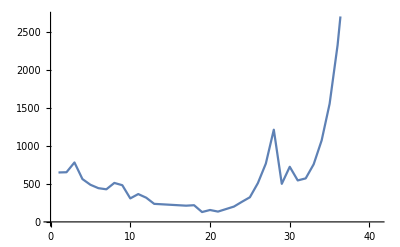
{False,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

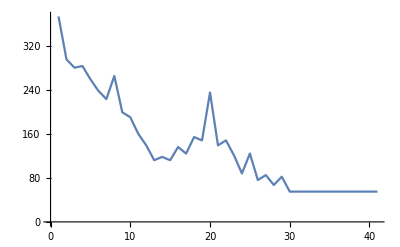
{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

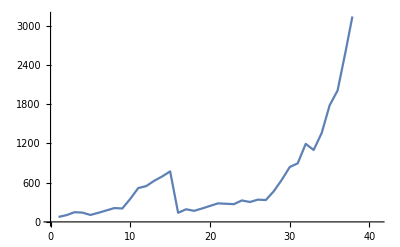
{False,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

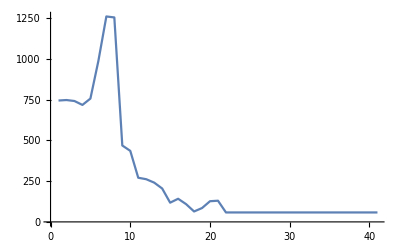
{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

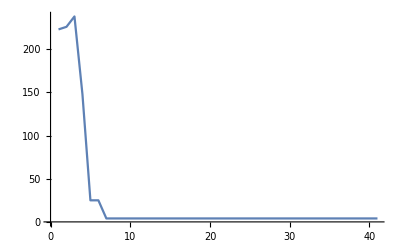
{False,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

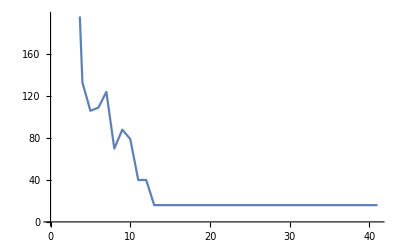
{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

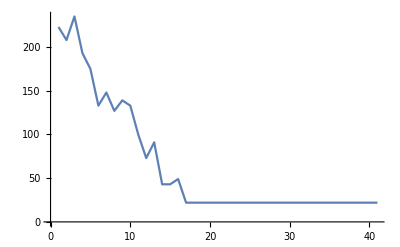
{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

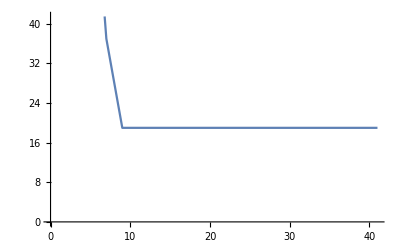
{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

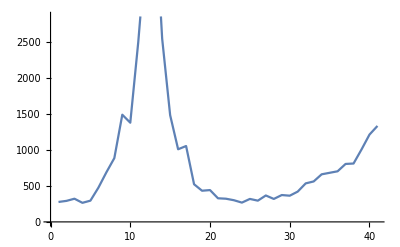
{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

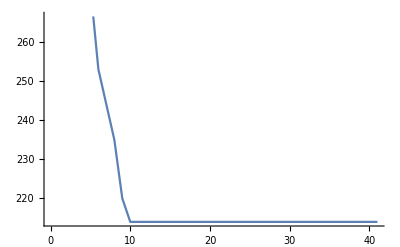
{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

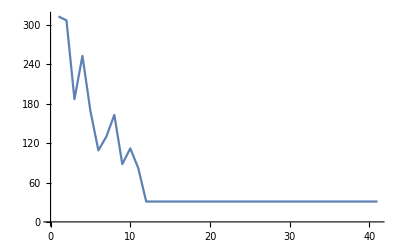
{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

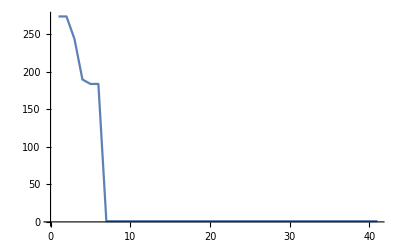
{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

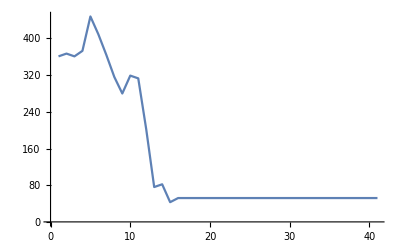
{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

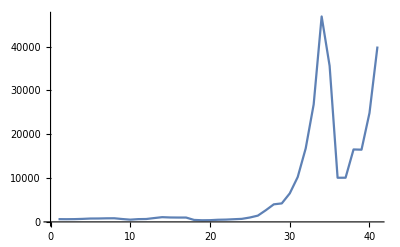
{False,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

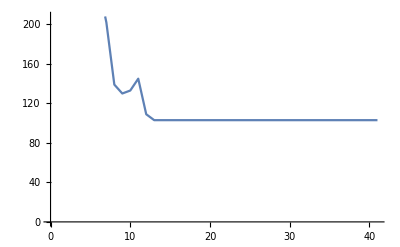
{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

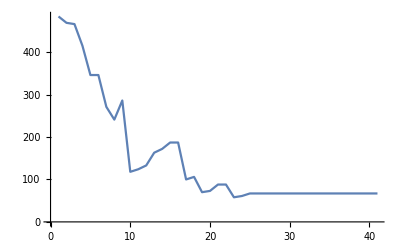
{False,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

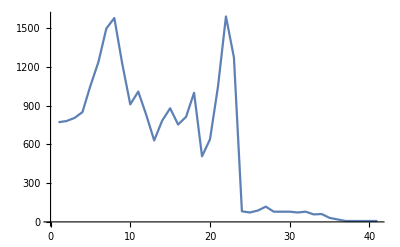
{False,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

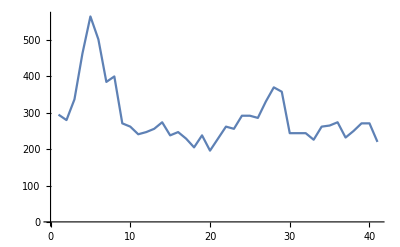
{False,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

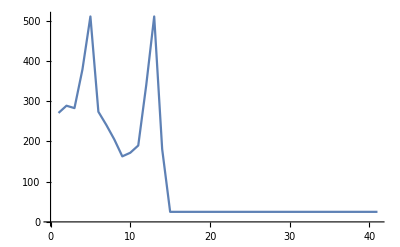
{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

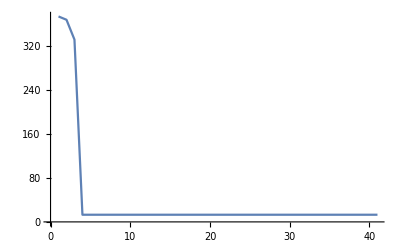
{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

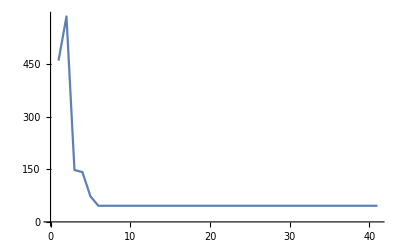
{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

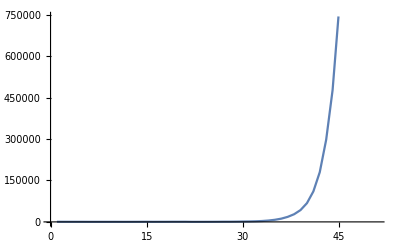
{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

### Training Attempt #5: 5000 random SK expressions, depth 10, halted if SKHalt[40]==True. NoHalt dataset same length as Halt dataset. Using raw string. (Same as #1, but larger dataset) Worse than 1 (slightly).

```mathematica
lengths = x;
```

```mathematica
NoHalt = Select[lengths,#[[2]]==False&];
Halt = Select[lengths,#[[2]]==True&];
Length[NoHalt]
Length[Halt]
```

862

4138

```mathematica
HaltTrain = RandomSample[Halt,Length[NoHalt]];
TrainingData = Join[HaltTrain,NoHalt];
TrainingData2 = ConvertSKTableToString[TrainingData];
Length[TrainingData2]
```

1724

```mathematica
HaltClassifier1 = Classify[TrainingData2]
```

ClassifierFunction[…]

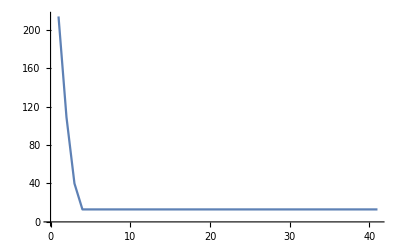
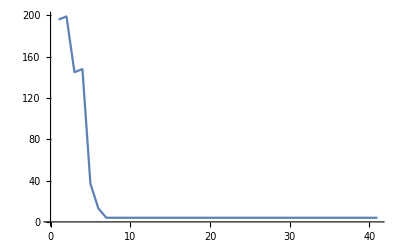
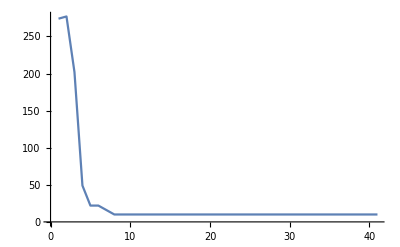
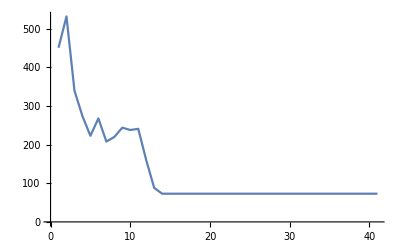
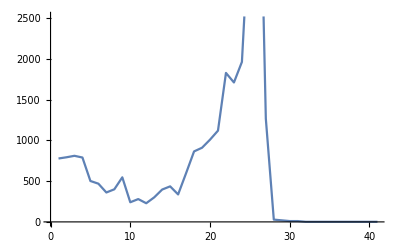
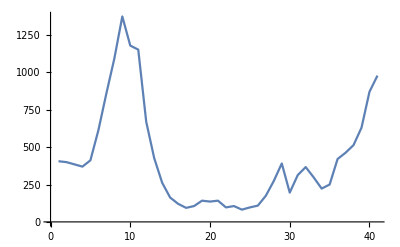
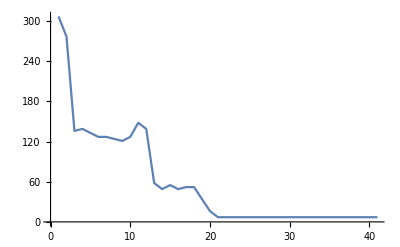
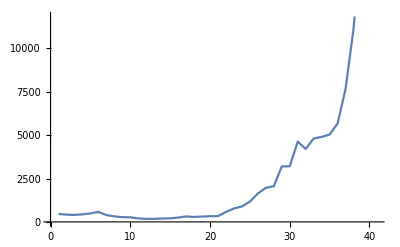
{{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False}}

```mathematica
Table[TestClassifier[HaltClassifier1,TrainingData2],10]
```

#### Classifier test:

```mathematica
Table[TestClassifier[HaltClassifier1,TrainingData2],10]
```

{False,-Graphics-}

{False,-Graphics-,False}

{True,-Graphics-,False}

{True,-Graphics-}

{True,-Graphics-}

{True,-Graphics-}

{True,-Graphics-}

```mathematica
SKGrid[k[s[k[k[k[k[s[s[k[k[k[k][s[s[k[k[s[s][k[k[k][k[k[s[k]]]]][k[k]][s]]]]][k[s]]]][k[s[k[k][k[s[k[s[s][s[s]]]][s[s[k]]]][k]]][s[s[k[k]]]][k[k]]]][s[k[s[s[k][s[k][k]][s[k]]]][k[s[k]][k]]][s[k]][k]]][s[k[s]][k]][k[k[k]]]][k]]]]]]][k[s[s[k[s[s]]]]][s]]][k[s]]]]
```

-Graphics-

```mathematica
GenerateTable[depth_,iterations_,number_]:=Module[{exprs},
exprs = Monitor[Table[RandomSKExpr[depth],{n,number}],n];
lengths = Monitor[Table[exprs[[n]]-> SKHalt[exprs[[n]],iterations],{n,number}],n];
Return[lengths]
]
```

```mathematica
Monitor[Flatten[Table[GenerateTable[n,40,200],{n,1,10}]],n]
```

{k[s]→True,s[k]→True,1997,s[k[k[s[k[k[s[k[s[s[s[k][k[k[k[s[k[s[k[s[k[s][s[s[k]][k[s]][s]]][s[s][s]][k[k]]]]][k[k[s][k[s]][s]][s[s[k]][k]][s[k]][k]]]]]]][s[s[k[k[s[k[k[s[k]][s[k[k]]]]]]][s[k[k[s][s]]][k]][s[k[s]][s]]]]]]][s[k][k[s]][s]][s[s[s]]][s[k]][k]]]]]][s[k][k[s[s]][k]][s[k]][s]]]][k[k]]]→True}
 |  |  |  |

### ML Advice - from Matteo Salvarazza

ML Advice
How to represent data?
- Sequence of ‘sequences’
Can you find a mapping between one of the sequences and an integer? 
	--> base4 encoding (this will be unique)
		Problem: input size is unbounded.
		Solution: Generate training set, use base4 encoding, look at maximum
	--> or ?strings or something?
		Advantages - it captures subtleties of combinators
			Alternatively, use base4 and padding - then they become ‘images’ (matrices).
				In this case, still use RNN - a sequence of n-dimensional vectors where n is the longest element in training set.
	--> or trees?
		Advantages - purest method of representing combinators.
- or just initial SKcombinator (‘sequence’)

How to creat

Type of dataset? (50:50 halt:no halt or actual distribution?)
	Training set *must* be balanced, even if real world not balanced.

Ratio of data within dataset? (distribution of examples belonging to specific class)
	Usually unimportant - just experiment. Generate a *balanced training set* and an *unbalanced training set*

What model to use?
	Recurrent neural net.
		base4 format - sequence classification problem.
			Usual entry-level problem - sentiment analysis. Take this architecture and experiment.
			Look at tutorials about sentiment analysis (simple - this problem is much harder)

Ensure {no --> very few} combinators halt within the given training set, otherwise problem is trivial.
	(e.g. size 10 vector - [[9]]!=[[10]] - experiment)


First thing to try: do the initial base 4 encoding, generate (some large n) training sets, find vocabulary size and check for presence of duplicates. If super sparse (large vocabulary, most tokens only appear once), this is bad
	--> try sequence encoding, with padding method. (Problem - a lot of padding. This is also bad. Experiment with different initial evolution lengths)
(alternatively, try RNN with just initial state - will solve all of the above problems, but probably won’t work. 0th thing to try - training example just a sequence of {chars/base4 numbers})

### Neural Net Attempt #1: Recurrent Neural Network, Raw String. SKCombinators_RNN_Raw_String.nb

Unsuccessful - no better than coin flipping. (Markov method earlier is better)

### Neural Net Attempt #2 - Preprocessing: Find vocabulary.